```mathematica
(* Reissner-Nordstrom AdS with M = 0 Q = 0 *)
```

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[(1-2M/r[t]+Q^2/r[t]^2+r[t]^2/l^2)-D[r[t],t]^2/(1-2M/r[t]+Q^2/r[t]^2+r[t]^2/l^2),r[t],t]
```

2 (-Q^2/r[t]^3+M/r[t]^2-(M r'[t]^2)/((-2 M+Q^2/r[t]+r[t]+r[t]^3/l^2)^2)+(r[t] (1+((l^6 Q^2-l^4 r[t]^4) r'[t]^2)/((l^2 Q^2-2 l^2 M r[t]+l^2 r[t]^2+r[t]^4)^2)))/l^2+r''[t]/(1+Q^2/r[t]^2-(2 M)/r[t]+r[t]^2/l^2))==0

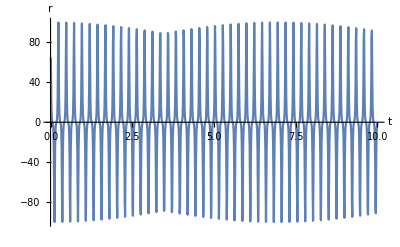

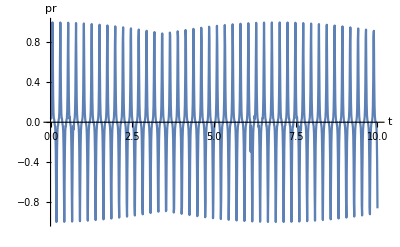

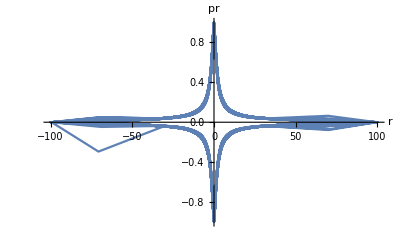

```mathematica
Block[
{lapsef,r1,r2,pr,rdot,t1},
lapsef[M_,Q_,l_,r_]:=1-2M/r+Q^2/r^2+r^2/l^2;
r1[M1_,Q1_,l1_,rs_]:=NDSolveValue[{2 (-Q^2/r[t]^3+M/r[t]^2-(M r'[t]^2)/((-2 M+Q^2/r[t]+r[t]+r[t]^3/l^2)^2)+(r[t] (1+((l^6 Q^2-l^4 r[t]^4) r'[t]^2)/((l^2 Q^2-2 l^2 M r[t]+l^2 r[t]^2+r[t]^4)^2)))/l^2+r''[t]/(1+Q^2/r[t]^2-(2 M)/r[t]+r[t]^2/l^2))==0/.{M->M1,Q->Q1,l->l1},r'[0]==0,r[0]==rs },r[t],{t,0,10}];
r2[t1_,M_,Q_,l_,rs_]:=r1[M,Q,l,rs]/.{t->t1};
rdot[t_,M_,Q_,l_,rs_]:=D[r2[t1,M,Q,l,rs],t1]/.{t1->t};
pr[t_,M_,Q_,l_,rs_]:=rdot[t,M,Q,l,rs]/Sqrt[lapsef[M,Q,l,r2[t,M,Q,l,rs]]^3-rdot[t,M,Q,l,rs]^2lapsef[M,Q,l,r2[t,M,Q,l,rs]]];
Print[ListLinePlot[Table[{i,Re[r2[i,0,0,1,100]]},{i,0.01,10,0.01}],AxesLabel->{t,r}]];
Print[ListLinePlot[Table[{i,Im[pr[i,0,0,1,100]]},{i,0.01,10,0.01}],AxesLabel->{t,pr}]];
Print[ListLinePlot[Table[{Re[r2[i,0,0,1,100]],Im[pr[i,0,0,1,100]]},{i,0.01,10,0.01}],AxesLabel->{r,pr}]];
]
```